## CO18-110231 Applied Dynamical Systems CO18-110233 Applied Dynamical Systems Lab

## Mathematica examples

## Part 2: A first look at ordinary differential equations (ODEs)

### First example

```mathematica
DSolve[D[x[t],t]==a x[t],x[t],t]
```

{{x[t]→ⅇ^(a t) C[1]}}

```mathematica
DSolve[D[x[t],t]==a x[t] - b x[t]^2,x[t],t]
```

{{x[t]→(a ⅇ^(a t+a C[1]))/(1+b ⅇ^(a t+a C[1]))}}

### More detailed discussion

```mathematica
fp = Solve[a x[t] - b x[t]^2==0,x[t]]
```

{{x[t]→0},{x[t]→a/b}}

```mathematica
sol1 = NDSolve[{D[x[t],t]==a x[t] - b x[t]^2 /. {a-> 0.3,b-> 0.6} ,x[0]==0.3},x[t],{t,0,20}]
```

{{x[t]→InterpolatingFunction[…][t]}}

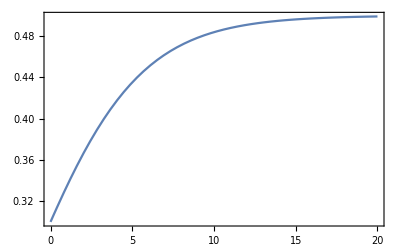

```mathematica
Plot[x[t] /. sol1, {t,0,20},Frame->True,PlotRange->All]
```

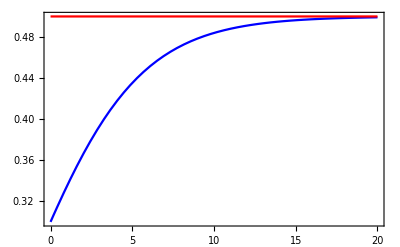

```mathematica
Plot[{x[t] /. sol1, x[t] /. fp[[2]] /.  {a-> 0.3,b-> 0.6}}, {t,0,20},Frame->True,PlotRange->All,PlotStyle->{Blue,Red}]
```

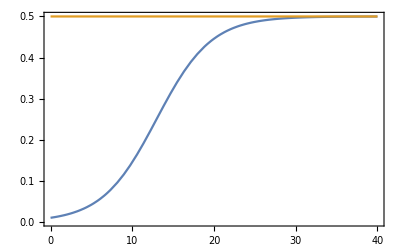

```mathematica
sol2 = NDSolve[{D[x[t],t]==a x[t] - b x[t]^2 /. {a-> 0.3,b-> 0.6} ,x[0]==0.01},x[t],{t,0,40}];
Plot[{x[t] /. sol2, x[t] /. fp[[2]] /.  {a-> 0.3,b-> 0.6}}, {t,0,40},Frame->True]
```

### Specific example

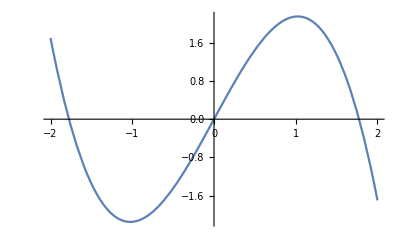

```mathematica
Plot[r x - x^3 /. r-> 3,{x,-2,2}]
```

### Fixed points and their stability

```mathematica
t1 = Solve[ r x - x^3 ==0,x]
```

{{x→-1.77482},{x→0.},{x→1.77482}}

```mathematica
D[r x - x^3,x]
```

3.15-3 x^2

```mathematica
help1 = D[r x - x^3,x] /. t1  /. r->3
```

{-6.3,3,-6.3}

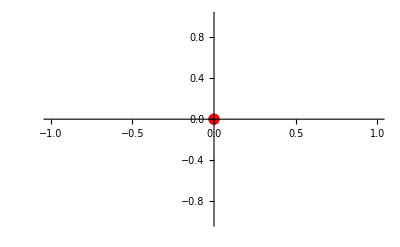

```mathematica
ListPlot[{{x /. t1[[2]] /. r->3,0}},PlotStyle->{{AbsolutePointSize[8],Red}}]
```

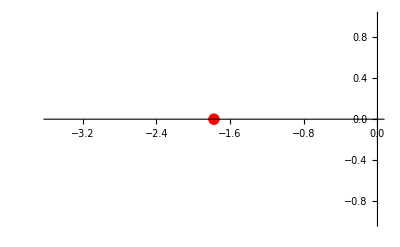
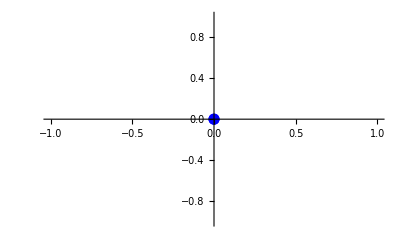
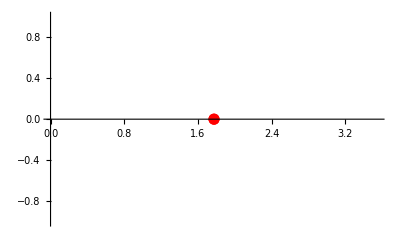

```mathematica
help2 = Table[If[help1[[j]]< 0, ListPlot[{{x /. t1[[j]] /. r->3,0}},PlotStyle->{{AbsolutePointSize[8],Red}}],ListPlot[{{x /. t1[[j]]/. r->3,0}},PlotStyle->{{AbsolutePointSize[8],Blue}}]],{j,1,Length[help1]}]
```

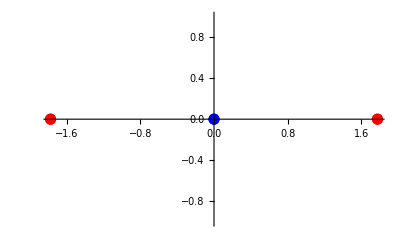

```mathematica
Show[help2,PlotRange->All]
```

```mathematica
insertStability[fun_,var_,range_]:=Module[{tmp1,tmp2,tmp3,tmp4,tmp5,tmp6},
tmp1 = Solve[ fun==0,var];
tmp2 = D[fun,var]; 
tmp3 = tmp2 /. tmp1;
tmp4 = Table[If[tmp3[[j]]< 0, ListPlot[{{var /. tmp1[[j]],0}},PlotStyle->{{AbsolutePointSize[8],Red}}],ListPlot[{{var /. tmp1[[j]],0}},PlotStyle->{{AbsolutePointSize[8],Blue}}]],{j,1,Length[tmp3]}];
tmp5 = Show[tmp4];
tmp6 = Plot[fun,{var,range[[1]],range[[2]]},PlotStyle->Black,Frame->True];
Show[tmp6,tmp5]]
```

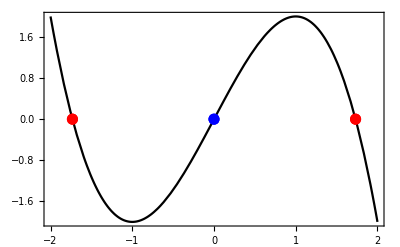

```mathematica
insertStability[3 x - x^3,x,{-2,2}]
```

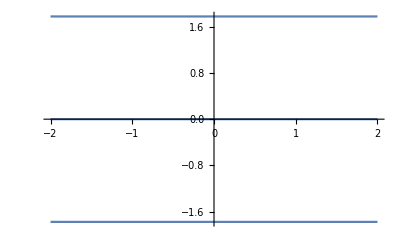

```mathematica
Plot[x /. t1,{r,-2,2}]
```

### Solutions of the ODE

```mathematica
sol0 = DSolve[{D[x[t],t]==r x[t]  - x[t]^3,x[0]==0.1} ,x[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{x[t]→(7.93725 2.71828^(3.15 t))/(√(6280.+20. 2.71828^(6.3 t)))}}

```mathematica
sol1 = NDSolve[{D[x[t],t]==r x[t]  - x[t]^3 /. r->3,x[0]==0.1},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[x[t] /. sol0[[2]] /.r-> 3,{t,0,10},Frame->True,PlotRange->All]
```

Part::partw: Part 2 of {{x[0.000204286]→0.100064}} does not exist.

ReplaceAll::reps: {{{x[0.000204286]→0.100064}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{x[0.204286]→0.189526}} does not exist.

ReplaceAll::reps: {{{x[0.204286]→0.189526}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 2 of {{x[0.408368]→0.355199}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {{{x[0.408368]→0.355199}}⟦2⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
sol1 = NDSolve[{D[x[t],t]==r x[t]  - x[t]^3 /. r->3,x[0]==0.1},x[t],{t,0,10}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
Plot[x[t] /. sol1 /.r-> 3,{t,0,10},Frame->True,PlotRange->All]
```

```mathematica
Plot[x[t] /. sol0[[2]] /.r-> 3,{t,0,10},Frame->True,PlotRange->All]
```

```mathematica
sol1 = NDSolve[{D[x[t],t]==r x[t]  - x[t]^3 /. r->3,x[0]==-0.1},x[t],{t,0,10}];
Plot[x[t] /. sol1,{t,0,10},Frame->True, PlotRange->All]
```